```mathematica
h1[b_,T_]:=b/Sqrt[2]*((1+2/π)*Sin[π/4/b]+(1-2/π)*Cos[π/4/b])
h2[t_,b_,T_]:=(Sin[π*t/T*(1-b)]+4*b*t/T*Cos[π*t/T*(1+b)])/(π*t/T*(1-(4*b*t/T)^2))
h[t_,b_,T_]:=If[t==0,1-b+4*b/π,If[t==T/4/b||t==-T/4/b,h1[b,T],h2[t,b,T]]]
N[h[4*10^(-3),1/2,1],10]
N[h[1/2+4*10^(-4),1/2,1],10]
Table[h[t,1/2,1],{t,-2,2,1/2}]
FindRoot[h[t,1/20,1],{t,22.1}]
3/(16*13)
```

1.136576129

0.5779180564

{2/(15 π),-1/(3 √2 π),-1/(3 π),(1+2/π)/(2 √2),1/2+2/π,(1+2/π)/(2 √2),-1/(3 π),-1/(3 √2 π),2/(15 π)}

{t→22.4379}

3/208

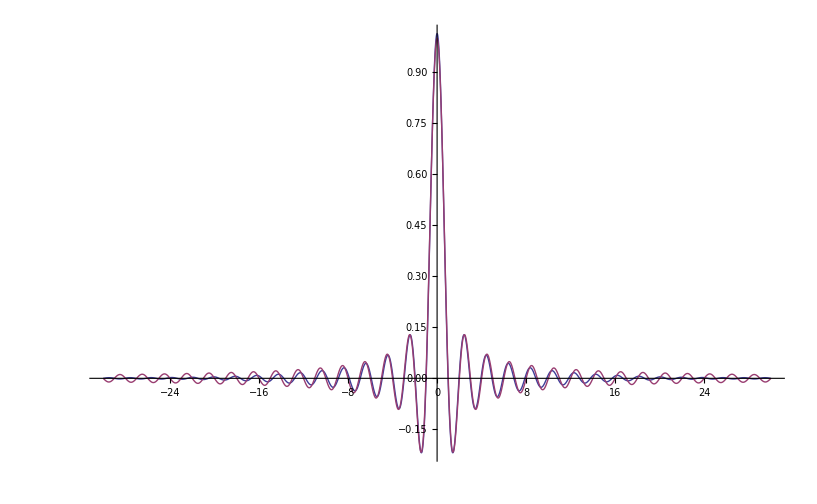

```mathematica
Plot[{h[t,1/20,1],Sinc[π*t]},{t,-30,30},PlotRange->All]
```

```mathematica
FullSimplify[Series[h2[t,b,T],{t,0,2}]]
FullSimplify[Series[h2[t,b,T],{t,T/4/b,2}]]
```

(1+b (-1+4/π))+(((-1+b)^3 π^3+96 b^2 (-b (-4+π)+π)-12 b (π+b π)^2) t^2)/(6 π T^2)+O[t]^3

b (-(2 Cos[((1+b) π)/(4 b)])/π+Sin[((1+b) π)/(4 b)])+(b ((12 b+π^2) Cos[((1+b) π)/(4 b)]+2 (1-2 b) π Sin[((1+b) π)/(4 b)]) (t-T/(4 b)))/(π T)+((6 b (-56 b^2+(1+(-4+b) b) π^2) Cos[((1+b) π)/(4 b)]-b π (24 (3-4 b) b+(3+b^2) π^2) Sin[((1+b) π)/(4 b)]) (t-T/(4 b))^2)/(6 π T^2)+O[t-T/(4 b)]^3

```mathematica
num[t_,b_,T_]:=Sin[π*t/T*(1-b)]+4*b*t/T*Cos[π*t/T*(1+b)]
FindRoot[num[t,1/2,1],{t,7}]
```

{t→6.9848}

```mathematica
Integrate[Sinc[π*t],{t,-5,5}]
```

(2 SinIntegral[5 π])/π

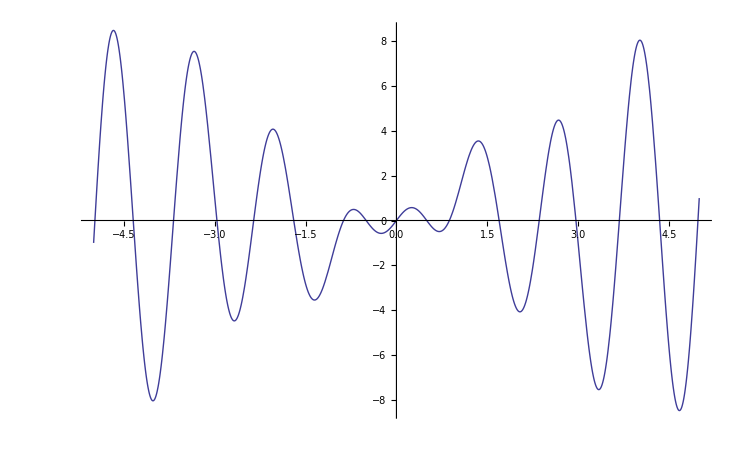

```mathematica
Plot[num[t,1/2,1],{t,-5,5}]
```

```mathematica
adc[t_,W_]:=W*HeavisidePi[4*t/W/Pi]
FourierTransform[adc[t,1/3],t,f]
```

1/36 √(π/2) Sinc[(f π)/24]

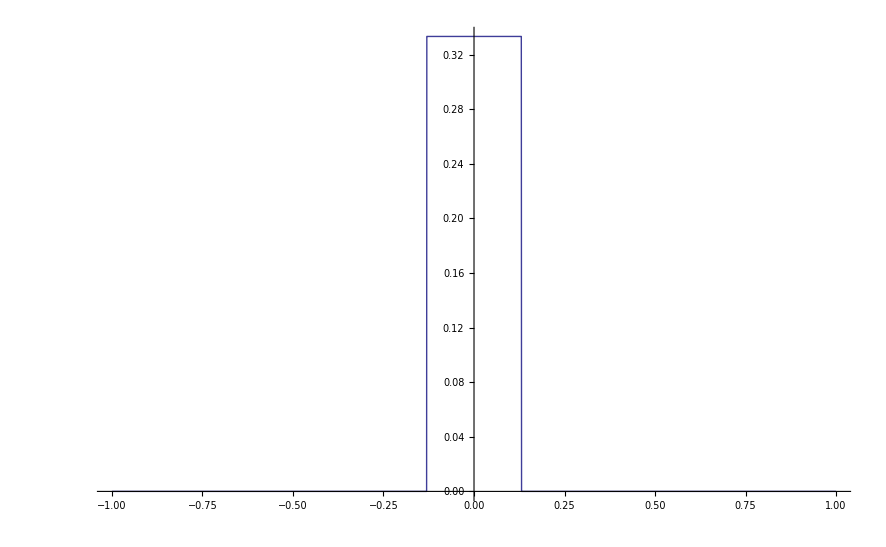

```mathematica
Plot[adc[t,1/3],{t,-1,1}]
```

```mathematica
FullSimplify[Convolve[adc[y,1/3],h2[y,1/3,1],y,t]]
```

$Aborted

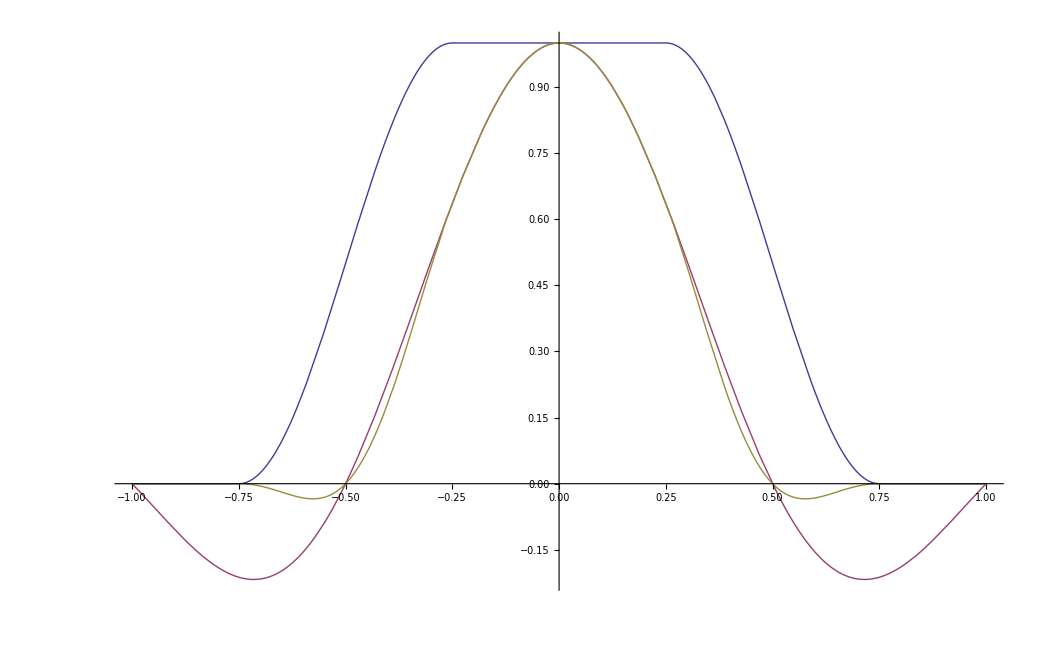

```mathematica
H[f_,b_,T_]:=If[Abs[f]<=(1-b)/2/T,T,If[Abs[f]<(1+b)/2/T,T*(1+Cos[Pi*T/b*(Abs[f]-(1-b)/2/T)])/2,0]]
Plot[{H[f,1/2,1],Sinc[Pi*f/0.5], H[f,1/2,1]*Sinc[Pi*f/0.5]},{f,-1,1}]
```

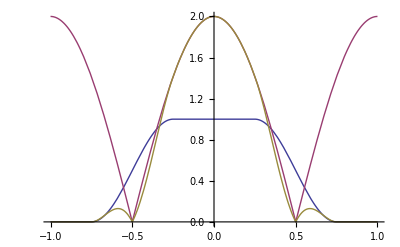

```mathematica
Plot[{H[f,1/2,1],Abs[1+Exp[2*Pi*I*f]], H[f,1/2,1]*Abs[1+Exp[2*Pi*I*f]]},{f,-1,1}]
```